# SpectralGap

## Fourier eigenvalues, spectral ordering, and large-n asymptotics

## Purpose

This notebook isolates the spectral-gap analysis from Chapter 2. It studies the averaging operator A_α, computes its Fourier eigenvalues and their magnitudes, verifies first-harmonic dominance, and investigates the logarithmic gap

γ_n(α)=log(μ_1/μ_2)

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions appear only in explanatory cells.

## 1. Definitions

```mathematica
ClearAll["Global`*"];

omega[n_Integer?Positive] := Exp[2 Pi I/n];

fourierVector[n_Integer?Positive, k_Integer] :=
  Table[omega[n]^(j k), {j, 0, n - 1}]/Sqrt[n];

fourierMatrix[n_Integer?Positive] :=
  Transpose@Table[fourierVector[n, k], {k, 0, n - 1}];

averagingMatrix[n_Integer?Positive, alpha_?NumericQ] :=
  Table[
    (1 - alpha) Boole[ell == j] + alpha Boole[ell == Mod[j + 1, n]],
    {j, 0, n - 1}, {ell, 0, n - 1}
  ];

lambda[n_Integer?Positive, k_Integer, alpha_] :=
  (1 - alpha) + alpha Exp[2 Pi I k/n];

mu[n_Integer?Positive, k_Integer, alpha_] :=
  Abs[lambda[n, k, alpha]];

gamma[n_Integer?Positive, alpha_] :=
  Log[mu[n, 1, alpha]/mu[n, 2, alpha]];
```

The averaging operator acts by

(A_α p)_j=(1-α)p_j+α p_(j+1)

```mathematica
nExample = 12;
alphaExample = 0.35;
A = averagingMatrix[nExample, alphaExample];
```

## 2. Fourier eigenvalues

For Fourier mode φ_k, the eigenvalue is

λ_k=(1-α)+α e^((2πik)/n)

```mathematica
eigenResidual[n_Integer?Positive, k_Integer, alpha_?NumericQ] := Module[
  {A, phi, lam},
  A = averagingMatrix[n, alpha];
  phi = fourierVector[n, k];
  lam = lambda[n, k, alpha];
  Max[Abs[N[A . phi - lam phi]]]
];

Table[
  {k, eigenResidual[nExample, k, alphaExample]},
  {k, 0, nExample - 1}
] // TableForm
```

0 | 0.
1 | 6.93889×10^-17
2 | 6.20634×10^-17
3 | 0.
4 | 3.10317×10^-17
5 | 5.59432×10^-17
6 | 0.
7 | 5.59432×10^-17
8 | 3.10317×10^-17
9 | 0.
10 | 6.20634×10^-17
11 | 6.93889×10^-17

## 3. Fourier diagonalization

```mathematica
F = fourierMatrix[nExample];
lambdaList = Table[lambda[nExample, k, alphaExample], {k, 0, nExample - 1}];
diagonalizedA = Chop[ConjugateTranspose[F] . A . F];
expectedDiagonal = DiagonalMatrix[lambdaList];
diagonalizationError = Max[Abs[Flatten[N[diagonalizedA - expectedDiagonal]]]];
diagonalizationQ = diagonalizationError < 10^-10;
```

```mathematica
diagonalizedA // MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.953109+0.175 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.825+0.303109 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.65+0.35 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.475+0.303109 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.346891+0.175 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.346891-0.175 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.475-0.303109 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.65-0.35 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.825-0.303109 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.953109-0.175 ⅈ)

```mathematica
diagonalizationError
```

3.43318×10^-16

```mathematica
diagonalizationQ
```

True

## 4. Eigenvalue magnitudes

The squared magnitude has the closed form

μ_k^2=(|λ_k|)^2=1-2α(1-α)(1-cos((2πk)/n))

```mathematica
muSquaredClosedForm[n_Integer?Positive, k_Integer, alpha_] :=
  1 - 2 alpha (1 - alpha) (1 - Cos[2 Pi k/n]);

magnitudeFormulaError[n_Integer?Positive, alpha_?NumericQ] :=
  Max@Table[
    Abs[N[mu[n, k, alpha]^2 - muSquaredClosedForm[n, k, alpha]]],
    {k, 0, n - 1}
  ];

magnitudeFormulaError[nExample, alphaExample]
```

1.38778×10^-16

```mathematica
magnitudeTable[n_Integer?Positive, alpha_?NumericQ] :=
  Table[{k, mu[n, k, alpha]}, {k, 0, n - 1}];

magnitudeTable[nExample, alphaExample] // TableForm
```

0 | 1.
1 | 0.969042
2 | 0.87892
3 | 0.738241
4 | 0.563471
5 | 0.388534
6 | 0.3
7 | 0.388534
8 | 0.563471
9 | 0.738241
10 | 0.87892
11 | 0.969042

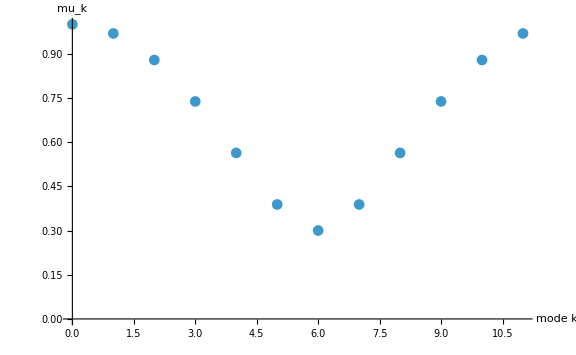

```mathematica
ListPlot[
  magnitudeTable[nExample, alphaExample],
  PlotMarkers -> Automatic,
  AxesLabel -> {"mode k", "mu_k"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 5. Symmetry and first-harmonic dominance

The magnitudes satisfy μ_k=μ_(n-k). For n≥5, the first harmonic has strictly larger magnitude than every mode k=2,…,n-2.

```mathematica
symmetryError[n_Integer?Positive, alpha_?NumericQ] :=
  Max@Table[
    Abs[N[mu[n, k, alpha] - mu[n, Mod[n - k, n], alpha]]],
    {k, 0, n - 1}
  ];

firstHarmonicDominanceMargin[n_Integer?Positive, alpha_?NumericQ] := Module[
  {higher},
  If[n < 5, Return[Missing["NotApplicable"]]];
  higher = Table[mu[n, k, alpha], {k, 2, n - 2}];
  mu[n, 1, alpha] - Max[higher]
];

firstHarmonicDominanceQ[n_Integer?Positive, alpha_?NumericQ] := Module[
  {margin = firstHarmonicDominanceMargin[n, alpha]},
  If[MissingQ[margin], margin, margin > 0]
];
```

```mathematica
symmetryError[nExample, alphaExample]
```

0.

```mathematica
Table[
  {n, firstHarmonicDominanceMargin[n, alphaExample], firstHarmonicDominanceQ[n, alphaExample]},
  {n, 5, 30}
] // TableForm
```

5 | 0.40742 | True
6 | 0.315448 | True
7 | 0.244175 | True
8 | 0.192744 | True
9 | 0.155335 | True
10 | 0.127553 | True
11 | 0.106462 | True
12 | 0.0901218 | True
13 | 0.077228 | True
14 | 0.0668878 | True
15 | 0.0584757 | True
16 | 0.0515447 | True
17 | 0.0457689 | True
18 | 0.0409068 | True
19 | 0.0367764 | True
20 | 0.0332386 | True
21 | 0.0301857 | True
22 | 0.0275334 | True
23 | 0.0252148 | True
24 | 0.0231763 | True
25 | 0.0213747 | True
26 | 0.0197747 | True
27 | 0.0183475 | True
28 | 0.017069 | True
29 | 0.0159194 | True
30 | 0.0148819 | True

## 6. The logarithmic spectral gap

γ_n(α)=log(μ_1/μ_2)>0

```mathematica
gapTable[alpha_?NumericQ, nMin_Integer?Positive, nMax_Integer?Positive] :=
  Table[{n, gamma[n, alpha]}, {n, nMin, nMax}];

gapTable[alphaExample, 5, 30] // TableForm
```

5 | 0.677365
6 | 0.444577
7 | 0.312288
8 | 0.231973
9 | 0.179518
10 | 0.143275
11 | 0.117128
12 | 0.0976139
13 | 0.0826457
14 | 0.0709029
15 | 0.0615148
16 | 0.0538874
17 | 0.047604
18 | 0.0423647
19 | 0.0379493
20 | 0.0341929
21 | 0.0309702
22 | 0.0281842
23 | 0.0257592
24 | 0.0236352
25 | 0.0217642
26 | 0.0201075
27 | 0.0186335
28 | 0.0173163
29 | 0.0161342
30 | 0.0150694

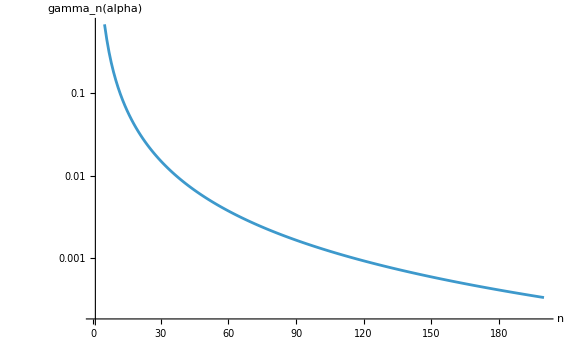

```mathematica
ListLogPlot[
  gapTable[alphaExample, 5, 200],
  Joined -> True,
  AxesLabel -> {"n", "gamma_n(alpha)"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 7. Large-n asymptotic

Chapter 2 gives the asymptotic behavior

γ_n(α)≈(6 π^2 α(1-α))/n^2

```mathematica
gapLeadingTerm[n_Integer?Positive, alpha_?NumericQ] :=
  6 Pi^2 alpha (1 - alpha)/n^2;

gapRatio[n_Integer?Positive, alpha_?NumericQ] :=
  gamma[n, alpha]/gapLeadingTerm[n, alpha];

scaledGap[n_Integer?Positive, alpha_?NumericQ] :=
  n^2 gamma[n, alpha];

asymptoticConstant[alpha_?NumericQ] :=
  6 Pi^2 alpha (1 - alpha);
```

```mathematica
Table[
  {
    n,
    gamma[n, alphaExample],
    gapLeadingTerm[n, alphaExample],
    gapRatio[n, alphaExample],
    scaledGap[n, alphaExample]
  },
  {n, 20, 200, 20}
] // TableForm
```

20 | 0.0341929 | 0.03368 | 1.01523 | 13.6772
40 | 0.00845172 | 0.00842001 | 1.00377 | 13.5227
60 | 0.00374848 | 0.00374223 | 1.00167 | 13.4945
80 | 0.00210698 | 0.002105 | 1.00094 | 13.4847
100 | 0.00134801 | 0.0013472 | 1.0006 | 13.4801
120 | 0.000935946 | 0.000935556 | 1.00042 | 13.4776
140 | 0.000687558 | 0.000687347 | 1.00031 | 13.4761
160 | 0.000526374 | 0.00052625 | 1.00023 | 13.4752
180 | 0.00041588 | 0.000415803 | 1.00019 | 13.4745
200 | 0.000336851 | 0.0003368 | 1.00015 | 13.474

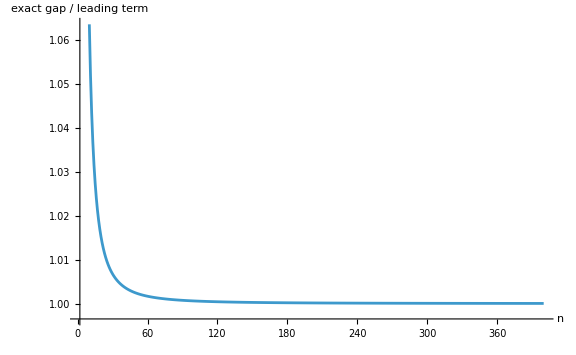

```mathematica
ListLinePlot[
  Table[{n, gapRatio[n, alphaExample]}, {n, 10, 400}],
  AxesLabel -> {"n", "exact gap / leading term"},
  PlotRange -> All,
  ImageSize -> Large
]
```

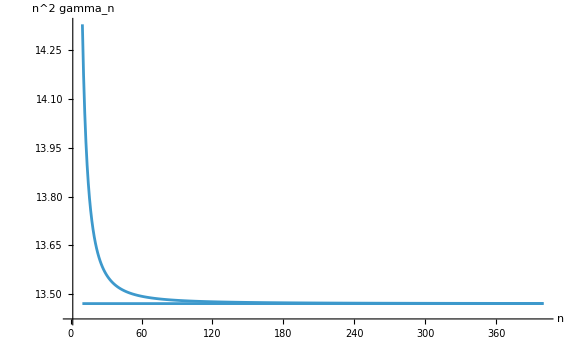

```mathematica
Show[
  ListLinePlot[
    Table[{n, scaledGap[n, alphaExample]}, {n, 10, 400}],
    AxesLabel -> {"n", "n^2 gamma_n"},
    PlotRange -> All
  ],
  Plot[
    asymptoticConstant[alphaExample],
    {n, 10, 400}
  ],
  ImageSize -> Large
]
```

## 8. Numerical asymptotic error

```mathematica
relativeAsymptoticError[n_Integer?Positive, alpha_?NumericQ] :=
  Abs[gamma[n, alpha] - gapLeadingTerm[n, alpha]]/gamma[n, alpha];

Table[
  {n, relativeAsymptoticError[n, alphaExample]},
  {n, 20, 300, 20}
] // TableForm
```

20 | 0.0150008
40 | 0.00375208
60 | 0.0016677
80 | 0.000938102
100 | 0.000600391
120 | 0.00041694
140 | 0.000306324
160 | 0.00023453
180 | 0.000185308
200 | 0.0001501
220 | 0.000124049
240 | 0.000104236
260 | 0.0000888165
280 | 0.0000765816
300 | 0.0000667111

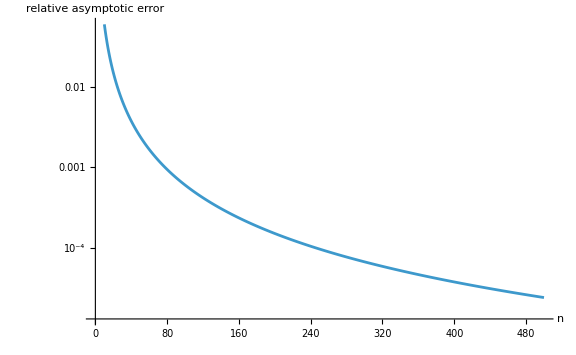

```mathematica
ListLogPlot[
  Table[{n, relativeAsymptoticError[n, alphaExample]}, {n, 10, 500}],
  Joined -> True,
  AxesLabel -> {"n", "relative asymptotic error"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 9. Dependence on alpha

The leading asymptotic coefficient 6 π^2 α(1-α) is symmetric about α=1/2 and is maximal there.

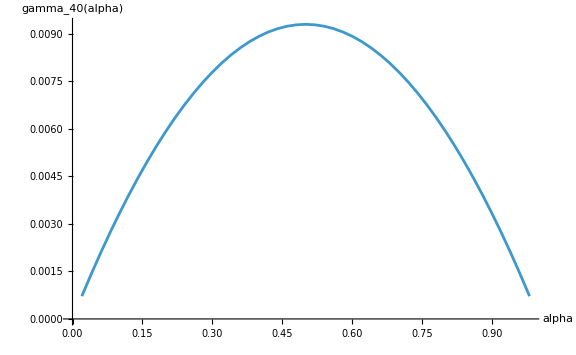

```mathematica
alphaGrid = Range[0.02, 0.98, 0.02];

ListLinePlot[
  Table[{alpha, gamma[40, alpha]}, {alpha, alphaGrid}],
  AxesLabel -> {"alpha", "gamma_40(alpha)"},
  PlotRange -> All,
  ImageSize -> Large
]
```

```mathematica
alphaSymmetryError[n_Integer?Positive, alpha_?NumericQ] :=
  Abs[N[gamma[n, alpha] - gamma[n, 1 - alpha]]];

Table[
  {alpha, alphaSymmetryError[40, alpha]},
  {alpha, {0.1, 0.2, 0.3, 0.4}}
] // TableForm
```

0.1 | 2.21177×10^-16
0.2 | 0.
0.3 | 0.
0.4 | 0.

```mathematica
optimalAlphaNumerical[n_Integer?Positive] := Module[{result},
  result = NMaximize[{gamma[n, alpha], 0 < alpha < 1}, alpha];
  {alpha /. Last[result], First[result]}
];

optimalAlphaNumerical[40]
```

{0.5,0.00930065}

## 10. Gap and suppression time

If a relative mode contribution is bounded by C e^(-m γ_n), then the iterations needed to reduce it below ϵ are estimated by

m≥(log(C/ϵ))/γ_n

```mathematica
suppressionTime[n_Integer?Positive, alpha_?NumericQ, C_?Positive, epsilon_?Positive] :=
  Ceiling[Log[C/epsilon]/gamma[n, alpha]];

Table[
  {
    n,
    suppressionTime[n, alphaExample, 2., 10^-3],
    suppressionTime[n, alphaExample, 2., 10^-3]/n^2
  },
  {n, 10, 100, 10}
] // TableForm
```

10 | 54 | 27/50
20 | 223 | 223/400
30 | 505 | 101/180
40 | 900 | 9/16
50 | 1408 | 352/625
60 | 2028 | 169/300
70 | 2762 | 1381/2450
80 | 3608 | 451/800
90 | 4567 | 4567/8100
100 | 5639 | 5639/10000

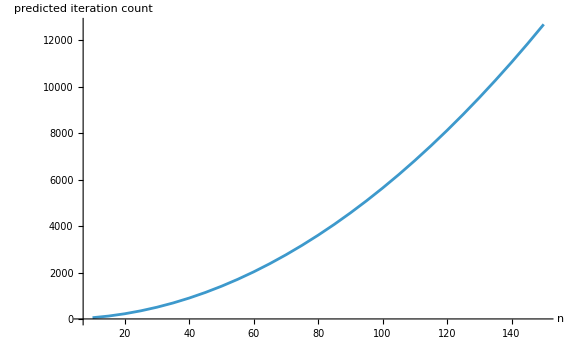

```mathematica
ListLinePlot[
  Table[
    {n, suppressionTime[n, alphaExample, 2., 10^-3]},
    {n, 10, 150, 5}
  ],
  AxesLabel -> {"n", "predicted iteration count"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 11. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[40];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[
      {alpha = 0.37, F, A, lambdas, diagonalError, eigenError, symmetry, margin, gapValue},
      F = fourierMatrix[n];
      A = averagingMatrix[n, alpha];
      lambdas = Table[lambda[n, k, alpha], {k, 0, n - 1}];
      diagonalError = Max[Abs[Flatten[N[
        ConjugateTranspose[F] . A . F - DiagonalMatrix[lambdas]
      ]]]];
      eigenError = Max@Table[eigenResidual[n, k, alpha], {k, 0, n - 1}];
      symmetry = symmetryError[n, alpha];
      margin = firstHarmonicDominanceMargin[n, alpha];
      gapValue = gamma[n, alpha];
      <|
        "n" -> n,
        "Fourier eigenvectors" -> TrueQ[eigenError < 10^-10],
        "Fourier diagonalization" -> TrueQ[diagonalError < 10^-10],
        "Magnitude symmetry" -> TrueQ[symmetry < 10^-10],
        "First-harmonic dominance" -> TrueQ[margin > 0],
        "Positive spectral gap" -> TrueQ[gapValue > 0]
      |>
    ],
    {n, 5, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
Length[DownValues[verificationReport]]
```

2

```mathematica
verificationReport[]
```

## Conclusion

The computations verify the spectral mechanism used in Chapter 2. The averaging operator is diagonal in the Fourier basis, the first harmonic dominates every higher nonconstant mode, and the logarithmic gap is positive. Its leading large-n behavior is proportional to n^-2, with coefficient 6 π^2 α(1-α).